```mathematica
(* Filename: Plot_example_in_experiment_2.nb *)
(* Ver. 0 (25-Apr-2023) *)
(*
This file is a program code in Mathematica to get plots in numerical experinemt 2.
*)
```

```mathematica
nn=2;
```

```mathematica
(***** In the following line, you need to set a path 
to the folder "experiment_2". *****)
datadir= "D:/.../experiment_2";
```

```mathematica
mydirA3 = StringJoin[datadir,"/By_w2_revA_SRCK2_avr_Al/dt=1_32/St3_Se16_Tr10000_B6400"];
mydirA4 = StringJoin[datadir,"/By_w2_revA_SRCK2_avr_Al/dt=1_16/St4_Se16_Tr10000_B6400"];
mydirA5 = StringJoin[datadir,"/By_w2_revA_SRCK2_avr_Al/dt=1_8/St5_Se16_Tr10000_B6400"];
mydirA7 = StringJoin[datadir,"/By_w2_revA_SRCK2_avr_Al/dt=1_4/St7_Se16_Tr10000_B6400"];
mydirA10 = StringJoin[datadir,"/By_w2_revA_SRCK2_avr_Al/dt=1_2/St10_Se16_Tr10000_B6400"];
(***)
mydirB3= StringJoin[datadir,"/By_wo2_srock2_Ab_values/dt=1_32/St3_Se16_Tr10000_B6400"];
mydirB4dt16 = StringJoin[datadir,"/By_wo2_srock2_Ab_values/dt=1_16/St4_Se16_Tr10000_B6400"];
mydirB5 = StringJoin[datadir,"/By_wo2_srock2_Ab_values/dt=1_8/St5_Se16_Tr10000_B6400"];
mydirB7 = StringJoin[datadir,"/By_wo2_srock2_Ab_values/dt=1_4/St7_Se16_Tr10000_B6400"];
mydirB10 = StringJoin[datadir,"/By_wo2_srock2_Ab_values/dt=1_2/St10_Se16_Tr10000_B6400"];
(***)
mydirC = StringJoin[datadir,"/By_wo2_SSDFMT/Set16_Tr10000_Batch6400"];
(***)
mydirD = StringJoin[datadir,"/By_wo2_Ef_AstabExpRK3/Set16_Tr10000_Batch6400"];
```

```mathematica
steplogleng=5; (* 4, 5 *)
stepPlotStart=1; (* 1, 2, 3 *)
```

```mathematica
numSet=16;(* 3, 16*)
ydim=nn;
```

```mathematica
dataA3=Table[1,{ii,1,ydim}];
For[ii=1, ii<=ydim, ii++,
basename[ii]=StringJoin["/expectfile",ToString[ii-1]];
filename[ii]=StringJoin["/Set_",ToString[1],basename[ii]];
dataA3[[ii]]=Import[mydirA3<>filename[ii],"Table"];
For[iiset = 2,iiset≤numSet,iiset++,
filename[ii]=StringJoin["/Set_",ToString[iiset],basename[ii]];
dataA3[[ii]][[1,2]] += Import[StringJoin[mydirA3,filename[ii]],"Table"][[1,2]];
];
dataA3[[ii]][[1,2]] /= numSet;
];
(***)
dataA4=Table[1,{ii,1,ydim}];
For[ii=1, ii<=ydim, ii++,
basename[ii]=StringJoin["/expectfile",ToString[ii-1]];
filename[ii]=StringJoin["/Set_",ToString[1],basename[ii]];
dataA4[[ii]]=Import[mydirA4<>filename[ii],"Table"];
For[iiset = 2,iiset≤numSet,iiset++,
filename[ii]=StringJoin["/Set_",ToString[iiset],basename[ii]];
dataA4[[ii]][[1,2]] += Import[StringJoin[mydirA4,filename[ii]],"Table"][[1,2]];
];
dataA4[[ii]][[1,2]] /= numSet;
];
(***)
dataA5=Table[1,{ii,1,ydim}];
For[ii=1, ii<=ydim, ii++,
basename[ii]=StringJoin["/expectfile",ToString[ii-1]];
filename[ii]=StringJoin["/Set_",ToString[1],basename[ii]];
dataA5[[ii]]=Import[mydirA5<>filename[ii],"Table"];
For[iiset = 2,iiset≤numSet,iiset++,
filename[ii]=StringJoin["/Set_",ToString[iiset],basename[ii]];
dataA5[[ii]][[1,2]] += Import[StringJoin[mydirA5,filename[ii]],"Table"][[1,2]];
];
dataA5[[ii]][[1,2]] /= numSet;
];
(***)
dataA7=Table[1,{ii,1,ydim}];
For[ii=1, ii<=ydim, ii++,
basename[ii]=StringJoin["/expectfile",ToString[ii-1]];
filename[ii]=StringJoin["/Set_",ToString[1],basename[ii]];
dataA7[[ii]]=Import[mydirA7<>filename[ii],"Table"];
For[iiset = 2,iiset≤numSet,iiset++,
filename[ii]=StringJoin["/Set_",ToString[iiset],basename[ii]];
dataA7[[ii]][[1,2]] += Import[StringJoin[mydirA7,filename[ii]],"Table"][[1,2]];
];
dataA7[[ii]][[1,2]] /= numSet;
];
(***)
dataA10=Table[1,{ii,1,ydim}];
For[ii=1, ii<=ydim, ii++,
basename[ii]=StringJoin["/expectfile",ToString[ii-1]];
filename[ii]=StringJoin["/Set_",ToString[1],basename[ii]];
dataA10[[ii]]=Import[mydirA10<>filename[ii],"Table"];
For[iiset = 2,iiset≤numSet,iiset++,
filename[ii]=StringJoin["/Set_",ToString[iiset],basename[ii]];
dataA10[[ii]][[1,2]] += Import[StringJoin[mydirA10,filename[ii]],"Table"][[1,2]];
];
dataA10[[ii]][[1,2]] /= numSet;
];
```

```mathematica
dataB3=Table[1,{ii,1,ydim}];
For[ii=1, ii<=ydim, ii++,
basename[ii]=StringJoin["/expectfile",ToString[ii-1]];
filename[ii]=StringJoin["/Set_",ToString[1],basename[ii]];
dataB3[[ii]]=Import[mydirB3<>filename[ii],"Table"];
For[iiset = 2,iiset≤numSet,iiset++,
filename[ii]=StringJoin["/Set_",ToString[iiset],basename[ii]];
dataB3[[ii]][[1,2]] += Import[StringJoin[mydirB3,filename[ii]],"Table"][[1,2]];
];
dataB3[[ii]][[1,2]] /= numSet;
];
(***)
dataB4dt16=Table[1,{ii,1,ydim}];
For[ii=1, ii<=ydim, ii++,
basename[ii]=StringJoin["/expectfile",ToString[ii-1]];
filename[ii]=StringJoin["/Set_",ToString[1],basename[ii]];
dataB4dt16[[ii]]=Import[mydirB4dt16<>filename[ii],"Table"];
For[iiset = 2,iiset≤numSet,iiset++,
filename[ii]=StringJoin["/Set_",ToString[iiset],basename[ii]];
dataB4dt16[[ii]][[1,2]] += Import[StringJoin[mydirB4dt16,filename[ii]],"Table"][[1,2]];
];
dataB4dt16[[ii]][[1,2]] /= numSet;
];
(***)
dataB5=Table[1,{ii,1,ydim}];
For[ii=1, ii<=ydim, ii++,
basename[ii]=StringJoin["/expectfile",ToString[ii-1]];
filename[ii]=StringJoin["/Set_",ToString[1],basename[ii]];
dataB5[[ii]]=Import[mydirB5<>filename[ii],"Table"];
For[iiset = 2,iiset≤numSet,iiset++,
filename[ii]=StringJoin["/Set_",ToString[iiset],basename[ii]];
dataB5[[ii]][[1,2]] += Import[StringJoin[mydirB5,filename[ii]],"Table"][[1,2]];
];
dataB5[[ii]][[1,2]] /= numSet;
];
(***)
dataB7=Table[1,{ii,1,ydim}];
For[ii=1, ii<=ydim, ii++,
basename[ii]=StringJoin["/expectfile",ToString[ii-1]];
filename[ii]=StringJoin["/Set_",ToString[1],basename[ii]];
dataB7[[ii]]=Import[mydirB7<>filename[ii],"Table"];
For[iiset = 2,iiset≤numSet,iiset++,
filename[ii]=StringJoin["/Set_",ToString[iiset],basename[ii]];
dataB7[[ii]][[1,2]] += Import[StringJoin[mydirB7,filename[ii]],"Table"][[1,2]];
];
dataB7[[ii]][[1,2]] /= numSet;
];
(***)
dataB10=Table[1,{ii,1,ydim}];
For[ii=1, ii<=ydim, ii++,
basename[ii]=StringJoin["/expectfile",ToString[ii-1]];
filename[ii]=StringJoin["/Set_",ToString[1],basename[ii]];
dataB10[[ii]]=Import[mydirB10<>filename[ii],"Table"];
For[iiset = 2,iiset≤numSet,iiset++,
filename[ii]=StringJoin["/Set_",ToString[iiset],basename[ii]];
dataB10[[ii]][[1,2]] += Import[StringJoin[mydirB10,filename[ii]],"Table"][[1,2]];
];
dataB10[[ii]][[1,2]] /= numSet;
];
```

```mathematica
dataC=Table[1,{ii,1,ydim}];
For[ii=1, ii<=ydim, ii++,
basename[ii]=StringJoin["/expectfile",ToString[ii-1]];
filename[ii]=StringJoin["/Set_",ToString[1],basename[ii]];
dataC[[ii]]=Import[mydirC<>filename[ii],"Table"];
For[iiset = 2,iiset≤numSet,iiset++,
filename[ii]=StringJoin["/Set_",ToString[iiset],basename[ii]];
dataC[[ii]][[1,2]] += Import[StringJoin[mydirC,filename[ii]],"Table"][[1,2]];
];
dataC[[ii]][[1,2]] /= numSet;
];
```

```mathematica
dataD=Table[1,{ii,1,ydim}];
For[ii=1, ii<=ydim, ii++,
basename[ii]=StringJoin["/expectfile",ToString[ii-1]];
filename[ii]=StringJoin["/Set_",ToString[1],basename[ii]];
dataD[[ii]]=Import[mydirD<>filename[ii],"Table"];
For[iiset = 2,iiset≤numSet,iiset++,
filename[ii]=StringJoin["/Set_",ToString[iiset],basename[ii]];
dataD[[ii]][[1,2]] += Import[StringJoin[mydirD,filename[ii]],"Table"][[1,2]];
];
dataD[[ii]][[1,2]] /= numSet;
];
```

```mathematica
ExactOdeExp={{{0,N[Exp[-100],16]}},{{0,N[Exp[-1],16]}}}
```

{{{0,3.720075976020836×10^-44}},{{0,0.3678794411714423}}}

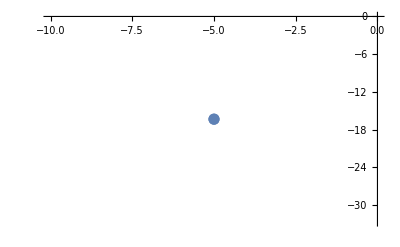

```mathematica
difflistA3={};
i=1;
difflistA3=Append[difflistA3,{dataA3[[1]]⟦i,1⟧,Log[2,(√(Sum[(dataA3[[id]]⟦i,2⟧-ExactOdeExp[[id]]⟦i,2⟧)^2,{id,1,ydim}]))/(√(Sum[(ExactOdeExp[[id]]⟦i,2⟧)^2,{id,1,ydim}]))]}];
tmpPlotExpA3=ListPlot[difflistA3,PlotStyle->PointSize[0.02]]
```

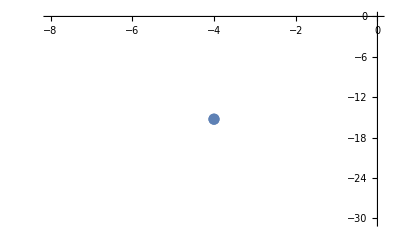

```mathematica
difflistA4={};
i=1;
difflistA4=Append[difflistA4,{dataA4[[1]]⟦i,1⟧,Log[2,(√(Sum[(dataA4[[id]]⟦i,2⟧-ExactOdeExp[[id]]⟦i,2⟧)^2,{id,1,ydim}]))/(√(Sum[(ExactOdeExp[[id]]⟦i,2⟧)^2,{id,1,ydim}]))]}];
tmpPlotExpA4=ListPlot[difflistA4,PlotStyle->PointSize[0.02]]
```

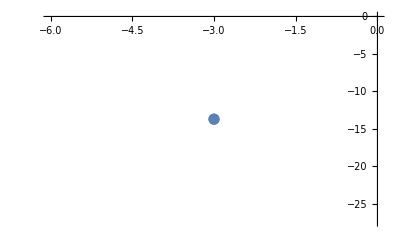

```mathematica
difflistA5={};
i=1;
difflistA5=Append[difflistA5,{dataA5[[1]]⟦i,1⟧,Log[2,(√(Sum[(dataA5[[id]]⟦i,2⟧-ExactOdeExp[[id]]⟦i,2⟧)^2,{id,1,ydim}]))/(√(Sum[(ExactOdeExp[[id]]⟦i,2⟧)^2,{id,1,ydim}]))]}];
tmpPlotExpA5=ListPlot[difflistA5,PlotStyle->PointSize[0.02]]
```

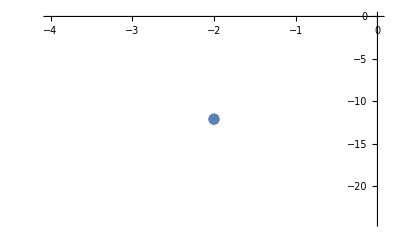

```mathematica
difflistA7={};
i=1;
difflistA7=Append[difflistA7,{dataA7[[1]]⟦i,1⟧,Log[2,(√(Sum[(dataA7[[id]]⟦i,2⟧-ExactOdeExp[[id]]⟦i,2⟧)^2,{id,1,ydim}]))/(√(Sum[(ExactOdeExp[[id]]⟦i,2⟧)^2,{id,1,ydim}]))]}];
tmpPlotExpA7=ListPlot[difflistA7,PlotStyle->PointSize[0.02]]
```

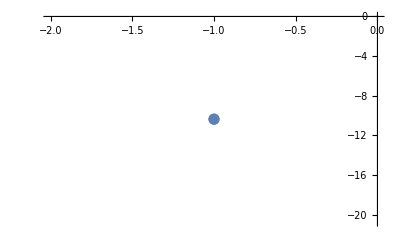

```mathematica
difflistA10={};
i=1;
difflistA10=Append[difflistA10,{dataA10[[1]]⟦i,1⟧,Log[2,(√(Sum[(dataA10[[id]]⟦i,2⟧-ExactOdeExp[[id]]⟦i,2⟧)^2,{id,1,ydim}]))/(√(Sum[(ExactOdeExp[[id]]⟦i,2⟧)^2,{id,1,ydim}]))]}];
tmpPlotExpA10=ListPlot[difflistA10,PlotStyle->PointSize[0.02]]
```

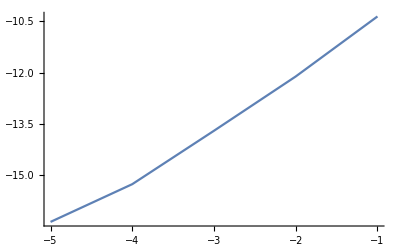

```mathematica
tmpList={difflistA3,difflistA4,difflistA5,difflistA7,difflistA10};
numOfList=Length[tmpList];
difflistAllA={};
For[i=1,i≤numOfList,i++,
difflistAllA=Append[difflistAllA,
tmpList[[i,1]]];
];
tmpPlotExpAllA=ListPlot[difflistAllA,Joined->True(*,PlotStyle->Dashing[{0.075,0.05}]*)]
```

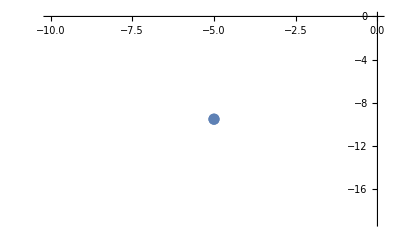

```mathematica
difflistB3={};
i=1;
difflistB3=Append[difflistB3,{dataB3[[1]]⟦i,1⟧,Log[2,(√(Sum[(dataB3[[id]]⟦i,2⟧-ExactOdeExp[[id]]⟦i,2⟧)^2,{id,1,ydim}]))/(√(Sum[(ExactOdeExp[[id]]⟦i,2⟧)^2,{id,1,ydim}]))]}];
tmpPlotExpB3=ListPlot[difflistB3,PlotStyle->PointSize[0.02]]
```

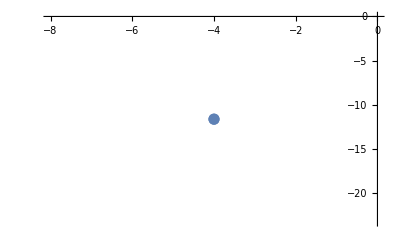

```mathematica
difflistB4dt16={};
i=1;
difflistB4dt16=Append[difflistB4dt16,{dataB4dt16[[1]]⟦i,1⟧,Log[2,(√(Sum[(dataB4dt16[[id]]⟦i,2⟧-ExactOdeExp[[id]]⟦i,2⟧)^2,{id,1,ydim}]))/(√(Sum[(ExactOdeExp[[id]]⟦i,2⟧)^2,{id,1,ydim}]))]}];
tmpPlotExpB4dt16=ListPlot[difflistB4dt16,PlotStyle->PointSize[0.02]]
```

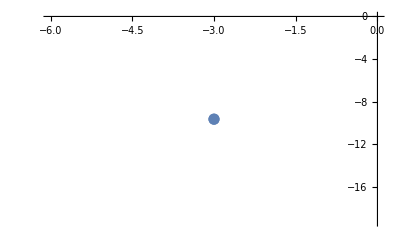

```mathematica
difflistB5={};
i=1;
difflistB5=Append[difflistB5,{dataB5[[1]]⟦i,1⟧,Log[2,(√(Sum[(dataB5[[id]]⟦i,2⟧-ExactOdeExp[[id]]⟦i,2⟧)^2,{id,1,ydim}]))/(√(Sum[(ExactOdeExp[[id]]⟦i,2⟧)^2,{id,1,ydim}]))]}];
tmpPlotExpB5=ListPlot[difflistB5,PlotStyle->PointSize[0.02]]
```

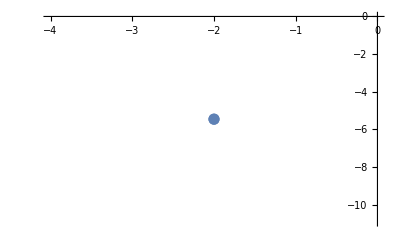

```mathematica
difflistB7={};
i=1;
difflistB7=Append[difflistB7,{dataB7[[1]]⟦i,1⟧,Log[2,(√(Sum[(dataB7[[id]]⟦i,2⟧-ExactOdeExp[[id]]⟦i,2⟧)^2,{id,1,ydim}]))/(√(Sum[(ExactOdeExp[[id]]⟦i,2⟧)^2,{id,1,ydim}]))]}];
tmpPlotExpB7=ListPlot[difflistB7,PlotStyle->PointSize[0.02]]
```

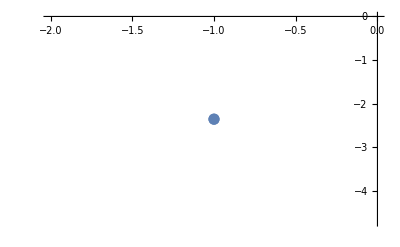

```mathematica
difflistB10={};
i=1;
difflistB10=Append[difflistB10,{dataB10[[1]]⟦i,1⟧,Log[2,(√(Sum[(dataB10[[id]]⟦i,2⟧-ExactOdeExp[[id]]⟦i,2⟧)^2,{id,1,ydim}]))/(√(Sum[(ExactOdeExp[[id]]⟦i,2⟧)^2,{id,1,ydim}]))]}];
tmpPlotExpB10=ListPlot[difflistB10,PlotStyle->PointSize[0.02]]
```

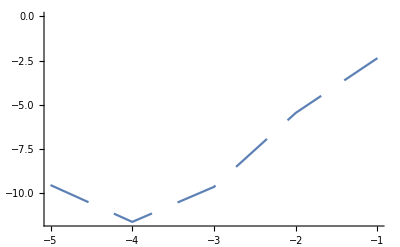

```mathematica
tmpList={difflistB3,difflistB4dt16,difflistB5,difflistB7,difflistB10};
numOfList=Length[tmpList];
difflistAllB={};
For[i=1,i≤numOfList,i++,
difflistAllB=Append[difflistAllB,
tmpList[[i,1]]];
];
tmpPlotExpAllB=ListPlot[difflistAllB,Joined->True,PlotStyle->Dashing[{0.075,0.05}]]
```

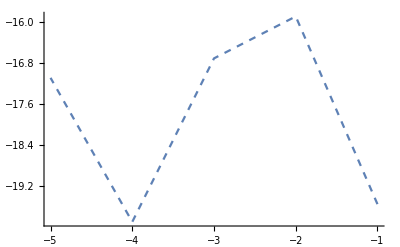

```mathematica
difflistC={};
iForExact=1;
For[i=stepPlotStart,i≤steplogleng,i++,difflistC=Append[difflistC,{dataC[[1]]⟦i,1⟧,Log[2,(√(Sum[(dataC[[id]]⟦i,2⟧-ExactOdeExp[[id]]⟦iForExact,2⟧)^2,{id,1,ydim}]))/(√(Sum[(ExactOdeExp[[id]]⟦iForExact,2⟧)^2,{id,1,ydim}]))]}];
];
tmpPlotExpC=ListPlot[difflistC,Joined->True,PlotStyle->Dashed]
```

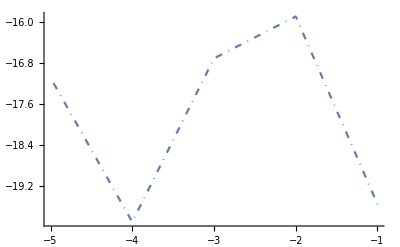

```mathematica
difflistD={};
iForExact=1;
For[i=stepPlotStart,i≤steplogleng,i++,difflistD=Append[difflistD,{dataD[[1]]⟦i,1⟧,Log[2,(√(Sum[(dataD[[id]]⟦i,2⟧-ExactOdeExp[[id]]⟦iForExact,2⟧)^2,{id,1,ydim}]))/(√(Sum[(ExactOdeExp[[id]]⟦iForExact,2⟧)^2,{id,1,ydim}]))]}];
];
tmpPlotExpD=ListPlot[difflistD,Joined->True,PlotStyle->DotDashed]
```

```mathematica
dataA3=Table[1,{ii,1,ydim}];
For[ii=1, ii<=ydim, ii++,
basename[ii]=StringJoin["/2momentfile",ToString[ii-1]];
filename[ii]=StringJoin["/Set_",ToString[1],basename[ii]];
dataA3[[ii]]=Import[mydirA3<>filename[ii],"Table"];
For[iiset = 2,iiset≤numSet,iiset++,
filename[ii]=StringJoin["/Set_",ToString[iiset],basename[ii]];
dataA3[[ii]][[1,2]] += Import[StringJoin[mydirA3,filename[ii]],"Table"][[1,2]];
];
dataA3[[ii]][[1,2]] /= numSet;
];
(***)
dataA4=Table[1,{ii,1,ydim}];
For[ii=1, ii<=ydim, ii++,
basename[ii]=StringJoin["/2momentfile",ToString[ii-1]];
filename[ii]=StringJoin["/Set_",ToString[1],basename[ii]];
dataA4[[ii]]=Import[mydirA4<>filename[ii],"Table"];
For[iiset = 2,iiset≤numSet,iiset++,
filename[ii]=StringJoin["/Set_",ToString[iiset],basename[ii]];
dataA4[[ii]][[1,2]] += Import[StringJoin[mydirA4,filename[ii]],"Table"][[1,2]];
];
dataA4[[ii]][[1,2]] /= numSet;
];
(***)
dataA5=Table[1,{ii,1,ydim}];
For[ii=1, ii<=ydim, ii++,
basename[ii]=StringJoin["/2momentfile",ToString[ii-1]];
filename[ii]=StringJoin["/Set_",ToString[1],basename[ii]];
dataA5[[ii]]=Import[mydirA5<>filename[ii],"Table"];
For[iiset = 2,iiset≤numSet,iiset++,
filename[ii]=StringJoin["/Set_",ToString[iiset],basename[ii]];
dataA5[[ii]][[1,2]] += Import[StringJoin[mydirA5,filename[ii]],"Table"][[1,2]];
];
dataA5[[ii]][[1,2]] /= numSet;
];
(***)
dataA7=Table[1,{ii,1,ydim}];
For[ii=1, ii<=ydim, ii++,
basename[ii]=StringJoin["/2momentfile",ToString[ii-1]];
filename[ii]=StringJoin["/Set_",ToString[1],basename[ii]];
dataA7[[ii]]=Import[mydirA7<>filename[ii],"Table"];
For[iiset = 2,iiset≤numSet,iiset++,
filename[ii]=StringJoin["/Set_",ToString[iiset],basename[ii]];
dataA7[[ii]][[1,2]] += Import[StringJoin[mydirA7,filename[ii]],"Table"][[1,2]];
];
dataA7[[ii]][[1,2]] /= numSet;
];
(***)
dataA10=Table[1,{ii,1,ydim}];
For[ii=1, ii<=ydim, ii++,
basename[ii]=StringJoin["/2momentfile",ToString[ii-1]];
filename[ii]=StringJoin["/Set_",ToString[1],basename[ii]];
dataA10[[ii]]=Import[mydirA10<>filename[ii],"Table"];
For[iiset = 2,iiset≤numSet,iiset++,
filename[ii]=StringJoin["/Set_",ToString[iiset],basename[ii]];
dataA10[[ii]][[1,2]] += Import[StringJoin[mydirA10,filename[ii]],"Table"][[1,2]];
];
dataA10[[ii]][[1,2]] /= numSet;
];
```

```mathematica
dataB3=Table[1,{ii,1,ydim}];
For[ii=1, ii<=ydim, ii++,
basename[ii]=StringJoin["/2momentfile",ToString[ii-1]];
filename[ii]=StringJoin["/Set_",ToString[1],basename[ii]];
dataB3[[ii]]=Import[mydirB3<>filename[ii],"Table"];
For[iiset = 2,iiset≤numSet,iiset++,
filename[ii]=StringJoin["/Set_",ToString[iiset],basename[ii]];
dataB3[[ii]][[1,2]] += Import[StringJoin[mydirB3,filename[ii]],"Table"][[1,2]];
];
dataB3[[ii]][[1,2]] /= numSet;
];
(***)
dataB4dt16=Table[1,{ii,1,ydim}];
For[ii=1, ii<=ydim, ii++,
basename[ii]=StringJoin["/2momentfile",ToString[ii-1]];
filename[ii]=StringJoin["/Set_",ToString[1],basename[ii]];
dataB4dt16[[ii]]=Import[mydirB4dt16<>filename[ii],"Table"];
For[iiset = 2,iiset≤numSet,iiset++,
filename[ii]=StringJoin["/Set_",ToString[iiset],basename[ii]];
dataB4dt16[[ii]][[1,2]] += Import[StringJoin[mydirB4dt16,filename[ii]],"Table"][[1,2]];
];
dataB4dt16[[ii]][[1,2]] /= numSet;
];
(***)
dataB5=Table[1,{ii,1,ydim}];
For[ii=1, ii<=ydim, ii++,
basename[ii]=StringJoin["/2momentfile",ToString[ii-1]];
filename[ii]=StringJoin["/Set_",ToString[1],basename[ii]];
dataB5[[ii]]=Import[mydirB5<>filename[ii],"Table"];
For[iiset = 2,iiset≤numSet,iiset++,
filename[ii]=StringJoin["/Set_",ToString[iiset],basename[ii]];
dataB5[[ii]][[1,2]] += Import[StringJoin[mydirB5,filename[ii]],"Table"][[1,2]];
];
dataB5[[ii]][[1,2]] /= numSet;
];
(***)
dataB7=Table[1,{ii,1,ydim}];
For[ii=1, ii<=ydim, ii++,
basename[ii]=StringJoin["/2momentfile",ToString[ii-1]];
filename[ii]=StringJoin["/Set_",ToString[1],basename[ii]];
dataB7[[ii]]=Import[mydirB7<>filename[ii],"Table"];
For[iiset = 2,iiset≤numSet,iiset++,
filename[ii]=StringJoin["/Set_",ToString[iiset],basename[ii]];
dataB7[[ii]][[1,2]] += Import[StringJoin[mydirB7,filename[ii]],"Table"][[1,2]];
];
dataB7[[ii]][[1,2]] /= numSet;
];
(***)
dataB10=Table[1,{ii,1,ydim}];
For[ii=1, ii<=ydim, ii++,
basename[ii]=StringJoin["/2momentfile",ToString[ii-1]];
filename[ii]=StringJoin["/Set_",ToString[1],basename[ii]];
dataB10[[ii]]=Import[mydirB10<>filename[ii],"Table"];
For[iiset = 2,iiset≤numSet,iiset++,
filename[ii]=StringJoin["/Set_",ToString[iiset],basename[ii]];
dataB10[[ii]][[1,2]] += Import[StringJoin[mydirB10,filename[ii]],"Table"][[1,2]];
];
dataB10[[ii]][[1,2]] /= numSet;
];
```

```mathematica
dataC=Table[1,{ii,1,ydim}];
For[ii=1, ii<=ydim, ii++,
basename[ii]=StringJoin["/2momentfile",ToString[ii-1]];
filename[ii]=StringJoin["/Set_",ToString[1],basename[ii]];
dataC[[ii]]=Import[mydirC<>filename[ii],"Table"];
For[iiset = 2,iiset≤numSet,iiset++,
filename[ii]=StringJoin["/Set_",ToString[iiset],basename[ii]];
dataC[[ii]][[1,2]] += Import[StringJoin[mydirC,filename[ii]],"Table"][[1,2]];
];
dataC[[ii]][[1,2]] /= numSet;
];
```

```mathematica
dataD=Table[1,{ii,1,ydim}];
For[ii=1, ii<=ydim, ii++,
basename[ii]=StringJoin["/2momentfile",ToString[ii-1]];
filename[ii]=StringJoin["/Set_",ToString[1],basename[ii]];
dataD[[ii]]=Import[mydirD<>filename[ii],"Table"];
For[iiset = 2,iiset≤numSet,iiset++,
filename[ii]=StringJoin["/Set_",ToString[iiset],basename[ii]];
dataD[[ii]][[1,2]] += Import[StringJoin[mydirD,filename[ii]],"Table"][[1,2]];
];
dataD[[ii]][[1,2]] /= numSet;
];
```

```mathematica
ExactOdeDis={{{0,0.00017114710700859314408326425399496292`16.}},{{0,0.13554872484529334896861160574`16.}}}
```

{{{0,0.0001711471070085931}},{{0,0.1355487248452933}}}

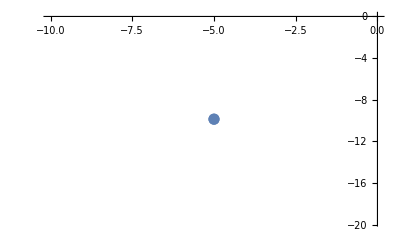

```mathematica
difflistA3={};
i=1;
difflistA3=Append[difflistA3,{dataA3[[1]]⟦i,1⟧,Log[2,(√(Sum[(dataA3[[id]]⟦i,2⟧-ExactOdeDis[[id]]⟦i,2⟧)^2,{id,1,ydim}]))/(√(Sum[(ExactOdeDis[[id]]⟦i,2⟧)^2,{id,1,ydim}]))]}];
tmpPlotDisA3=ListPlot[difflistA3,PlotStyle->PointSize[0.02]]
```

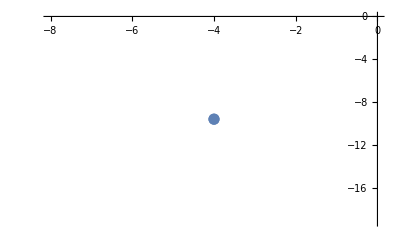

```mathematica
difflistA4={};
i=1;
difflistA4=Append[difflistA4,{dataA4[[1]]⟦i,1⟧,Log[2,(√(Sum[(dataA4[[id]]⟦i,2⟧-ExactOdeDis[[id]]⟦i,2⟧)^2,{id,1,ydim}]))/(√(Sum[(ExactOdeDis[[id]]⟦i,2⟧)^2,{id,1,ydim}]))]}];
tmpPlotDisA4=ListPlot[difflistA4,PlotStyle->PointSize[0.02]]
```

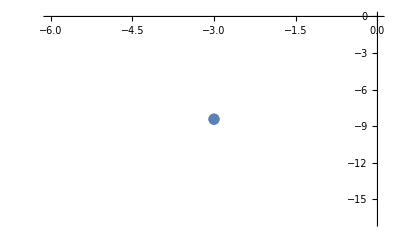

```mathematica
difflistA5={};
i=1;
difflistA5=Append[difflistA5,{dataA5[[1]]⟦i,1⟧,Log[2,(√(Sum[(dataA5[[id]]⟦i,2⟧-ExactOdeDis[[id]]⟦i,2⟧)^2,{id,1,ydim}]))/(√(Sum[(ExactOdeDis[[id]]⟦i,2⟧)^2,{id,1,ydim}]))]}];
tmpPlotDisA5=ListPlot[difflistA5,PlotStyle->PointSize[0.02]]
```

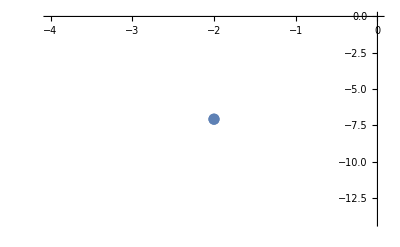

```mathematica
difflistA7={};
i=1;
difflistA7=Append[difflistA7,{dataA7[[1]]⟦i,1⟧,Log[2,(√(Sum[(dataA7[[id]]⟦i,2⟧-ExactOdeDis[[id]]⟦i,2⟧)^2,{id,1,ydim}]))/(√(Sum[(ExactOdeDis[[id]]⟦i,2⟧)^2,{id,1,ydim}]))]}];
tmpPlotDisA7=ListPlot[difflistA7,PlotStyle->PointSize[0.02]]
```

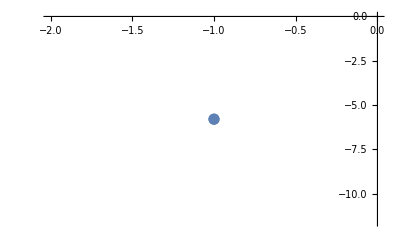

```mathematica
difflistA10={};
i=1;
difflistA10=Append[difflistA10,{dataA10[[1]]⟦i,1⟧,Log[2,(√(Sum[(dataA10[[id]]⟦i,2⟧-ExactOdeDis[[id]]⟦i,2⟧)^2,{id,1,ydim}]))/(√(Sum[(ExactOdeDis[[id]]⟦i,2⟧)^2,{id,1,ydim}]))]}];
tmpPlotDisA10=ListPlot[difflistA10,PlotStyle->PointSize[0.02]]
```

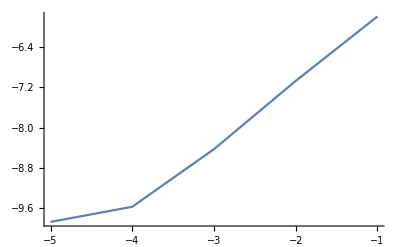

```mathematica
tmpList={difflistA3,difflistA4,difflistA5,difflistA7,difflistA10};
numOfList=Length[tmpList];
difflistAllA={};
For[i=1,i≤numOfList,i++,
difflistAllA=Append[difflistAllA,
tmpList[[i,1]]];
];
tmpPlotDisAllA=ListPlot[difflistAllA,Joined->True(*,PlotStyle->Dashing[{0.075,0.05}]*)]
```

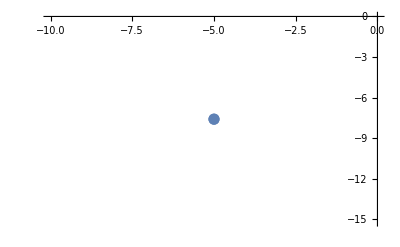

```mathematica
difflistB3={};
i=1;
difflistB3=Append[difflistB3,{dataB3[[1]]⟦i,1⟧,Log[2,(√(Sum[(dataB3[[id]]⟦i,2⟧-ExactOdeDis[[id]]⟦i,2⟧)^2,{id,1,ydim}]))/(√(Sum[(ExactOdeDis[[id]]⟦i,2⟧)^2,{id,1,ydim}]))]}];
tmpPlotDisB3=ListPlot[difflistB3,PlotStyle->PointSize[0.02]]
```

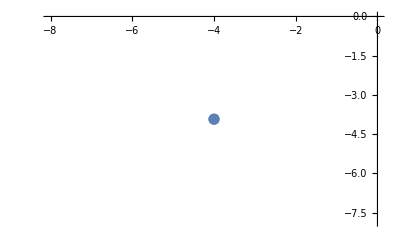

```mathematica
difflistB4dt16={};
i=1;
difflistB4dt16=Append[difflistB4dt16,{dataB4dt16[[1]]⟦i,1⟧,Log[2,(√(Sum[(dataB4dt16[[id]]⟦i,2⟧-ExactOdeDis[[id]]⟦i,2⟧)^2,{id,1,ydim}]))/(√(Sum[(ExactOdeDis[[id]]⟦i,2⟧)^2,{id,1,ydim}]))]}];
tmpPlotDisB4dt16=ListPlot[difflistB4dt16,PlotStyle->PointSize[0.02]]
```

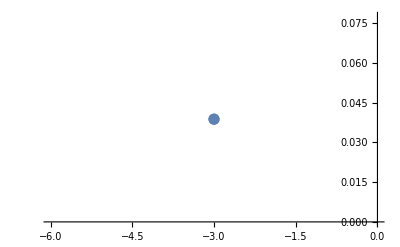

```mathematica
difflistB5={};
i=1;
difflistB5=Append[difflistB5,{dataB5[[1]]⟦i,1⟧,Log[2,(√(Sum[(dataB5[[id]]⟦i,2⟧-ExactOdeDis[[id]]⟦i,2⟧)^2,{id,1,ydim}]))/(√(Sum[(ExactOdeDis[[id]]⟦i,2⟧)^2,{id,1,ydim}]))]}];
tmpPlotDisB5=ListPlot[difflistB5,PlotStyle->PointSize[0.02]]
```

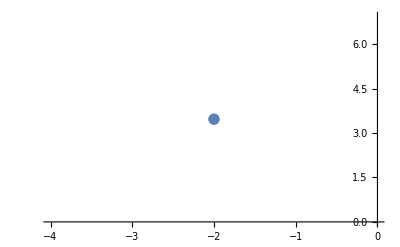

```mathematica
difflistB7={};
i=1;
difflistB7=Append[difflistB7,{dataB7[[1]]⟦i,1⟧,Log[2,(√(Sum[(dataB7[[id]]⟦i,2⟧-ExactOdeDis[[id]]⟦i,2⟧)^2,{id,1,ydim}]))/(√(Sum[(ExactOdeDis[[id]]⟦i,2⟧)^2,{id,1,ydim}]))]}];
tmpPlotDisB7=ListPlot[difflistB7,PlotStyle->PointSize[0.02]]
```

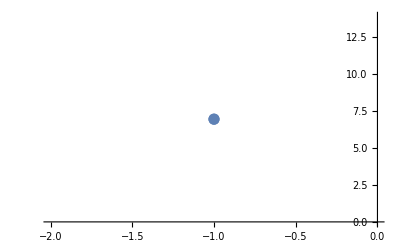

```mathematica
difflistB10={};
i=1;
difflistB10=Append[difflistB10,{dataB10[[1]]⟦i,1⟧,Log[2,(√(Sum[(dataB10[[id]]⟦i,2⟧-ExactOdeDis[[id]]⟦i,2⟧)^2,{id,1,ydim}]))/(√(Sum[(ExactOdeDis[[id]]⟦i,2⟧)^2,{id,1,ydim}]))]}];
tmpPlotDisB10=ListPlot[difflistB10,PlotStyle->PointSize[0.02]]
```

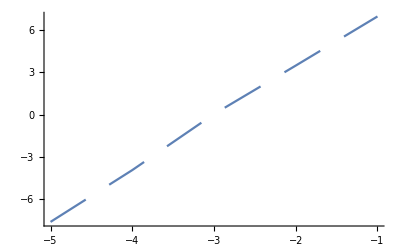

```mathematica
tmpList={difflistB3,difflistB4dt16,difflistB5,difflistB7,difflistB10};
numOfList=Length[tmpList];
difflistAllB={};
For[i=1,i≤numOfList,i++,
difflistAllB=Append[difflistAllB,
tmpList[[i,1]]];
];
tmpPlotDisAllB=ListPlot[difflistAllB,Joined->True,PlotStyle->Dashing[{0.075,0.05}]]
```

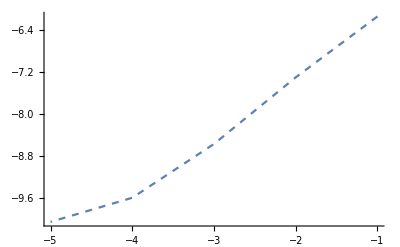

```mathematica
difflistC={};
iForExact=1;
For[i=stepPlotStart,i≤steplogleng,i++,difflistC=Append[difflistC,{dataC[[1]]⟦i,1⟧,Log[2,(√(Sum[(dataC[[id]]⟦i,2⟧-ExactOdeDis[[id]]⟦iForExact,2⟧)^2,{id,1,ydim}]))/(√(Sum[(ExactOdeDis[[id]]⟦iForExact,2⟧)^2,{id,1,ydim}]))]}];
];
tmpPlotDisC=ListPlot[difflistC,Joined->True,PlotStyle->Dashed]
```

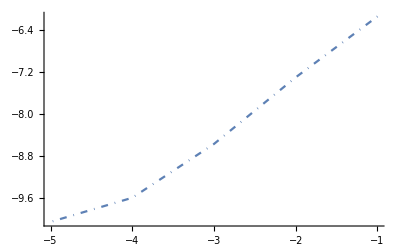

```mathematica
difflistD={};
iForExact=1;
For[i=stepPlotStart,i≤steplogleng,i++,difflistD=Append[difflistD,{dataD[[1]]⟦i,1⟧,Log[2,(√(Sum[(dataD[[id]]⟦i,2⟧-ExactOdeDis[[id]]⟦iForExact,2⟧)^2,{id,1,ydim}]))/(√(Sum[(ExactOdeDis[[id]]⟦iForExact,2⟧)^2,{id,1,ydim}]))]}];
];
tmpPlotDisD=ListPlot[difflistD,Joined->True,PlotStyle->DotDashed]
```

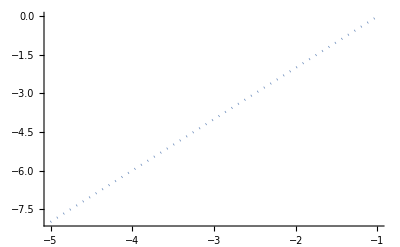

```mathematica
tmpRefSlope2=Plot[2x+2,{x,-5,-1},PlotStyle->Dotted]
```

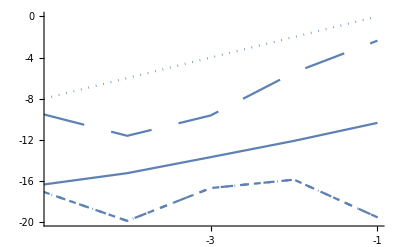

```mathematica
ll=0.03;
Show[tmpPlotExpAllA,tmpPlotExpAllB,tmpPlotExpC,tmpPlotExpD,tmpRefSlope2,PlotRange->{{-steplogleng+0.08,-1},{-20,0}},AxesOrigin->{-steplogleng,0},Ticks->{Table[{-1ii,ToString[-1ii],ll},{ii,1,6}],Union[Table[{-2ii,ToString[-2ii],ll},{ii,-1,10}],{{0,"0",ll}}]},BaseStyle->{14,FontFamily->"Helvetica"}]
```

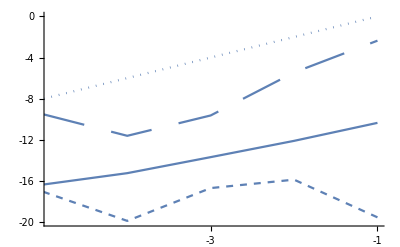

```mathematica
ll=0.03;
Show[tmpPlotExpAllA,tmpPlotExpAllB,tmpPlotExpC,(*tmpPlotExpD,*)tmpRefSlope2,PlotRange->{{-steplogleng+0.08,-1},{-20,0}},AxesOrigin->{-steplogleng,0},Ticks->{Table[{-1ii,ToString[-1ii],ll},{ii,1,6}],Union[Table[{-2ii,ToString[-2ii],ll},{ii,-1,10}],{{0,"0",ll}}]},BaseStyle->{14,FontFamily->"Helvetica"}]
```

```mathematica
tmpRefSlope2=Plot[2x+2,{x,-5,-1},PlotStyle->Dotted]
```

-Graphics-

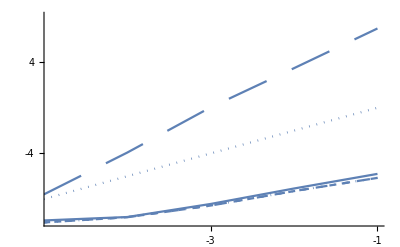

```mathematica
Show[tmpPlotDisAllA,tmpPlotDisAllB,tmpPlotDisC,tmpPlotDisD,tmpRefSlope2,PlotRange->{{-steplogleng+0.08,-1},{-10,8}},AxesOrigin->{-steplogleng,0},Ticks->{Table[{-1ii,ToString[-1ii],ll},{ii,1,6}],Union[Table[{-2ii,ToString[-2ii],ll},{ii,1,10}],{{0,"0",ll}},Table[{2ii,ToString[2ii],ll},{ii,1,10}]]},BaseStyle->{14,FontFamily->"Helvetica"}]
```

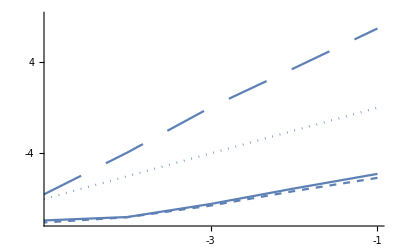

```mathematica
Show[tmpPlotDisAllA,tmpPlotDisAllB,tmpPlotDisC,(*tmpPlotDisD,*)tmpRefSlope2,PlotRange->{{-steplogleng+0.08,-1},{-10,8}},AxesOrigin->{-steplogleng,0},Ticks->{Table[{-1ii,ToString[-1ii],ll},{ii,1,6}],Union[Table[{-2ii,ToString[-2ii],ll},{ii,1,10}],{{0,"0",ll}},Table[{2ii,ToString[2ii],ll},{ii,1,10}]]},BaseStyle->{14,FontFamily->"Helvetica"}]
```